```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/chains/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/chains

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
intrachainAvail=Normal[DeleteDuplicates[ds[Take,"intrachain"]]];
isotropyAvail=Normal[DeleteDuplicates[ds[Take,"isotropy"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail,"intrachain"->intrachainAvail,"isotropy"->isotropyAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->2];

fs=22;
tckn=0.005;

(*If[B==-1.,inplt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->2.5];
ImageSize->240,
Joined->False,
PlotMarkers->{"●",10},
PlotStyle->If[B==1.,Orange,Purple],
Frame->True,Axes->False,
PlotRangeClipping->True,
ClippingStyle->Automatic,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
FrameTicksStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
FrameLabel->MaTeX@{"n","c_n/c_0"},
PlotRange->{{0,n-1},{0.75,1.05}},
AspectRatio->0.75,
PlotLegends->Placed[PointLegend[{Orange},{MaTeX["\\lambda = 1"]},LegendMarkerSize->12],{0.64,0.85}],
FrameTicks->{{LinTicks[0.5,1.5,0.1,2,TickLabelFunction->tlf],LinTicks[0.5,1.5,0.1,2,ShowTickLabels->False]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}},
Epilog->{
Inset[MaTeX["\\text{(b) }"],Scaled[{0.2,0.8}]],
Inset[MaTeX["(t\\text{--}J)"],Scaled[{0.71,0.67}]]
}
]];*)

plt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->
If[KK==1,
{"▲",12},
If[KK==0.1,
{"▼",12},
If[KK==0.01,
{"■",13},
{"●",10}
]]],
(*Mesh->15,*)
PlotStyle->If[KK==1.,
Lighter[Blend[{Red,Purple},0.25]],
If[KK==0.1,
Lighter[Blend[{Red,Purple},0.75]],
If[KK==0.01,
Purple,
Orange
]]],
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
(*InterpolationOrder->0,*)
PlotRange->{{0,n-1},{10^-17,9.9}},
PlotRangeClipping->True,
(*PlotLegends->Placed[Automatic,Right],*)
ClippingStyle->Automatic,
AspectRatio->0.85,
FrameLabel->MaTeX@{"n","c_n / c_0"},
(*Epilog->
Join[{
Inset[
MaTeX["\\text{(a) }"],
{3,-10}]
},
If[(*B==1.*)False,{
Inset[inplt,{4.5,-24},{1,1},13],
Text[Style["n",Black,fs,FontFamily->"CMU Serif"],{9.5,-37.5}],
Rotate[Text[Style["c_n / c_n",Black,fs,FontFamily->"CMU Serif"],{1.35,-28.25}],90Degree]
},{}]],*)
(*ScalingFunctions->"Log",*)
FrameTicks->{LinTicks[0,1,0.5,5],LinTicks[0,1,0.5,5,ShowTickLabels->False],LinTicks[-3,3,1,1],LinTicks[-3,3,1,1,ShowTickLabels->False]}
(*{{Table[{10^-l,If[Mod[l,2]==0,MaTeX[l],""]},{l,-10,20,1}],Table[{10^-l,""},{l,-10,20,1}]},{LinTicks[-30,30,10,10,TickLabelFunction->tlf],LinTicks[-30,30,10,10,ShowTickLabels->False]}}*)
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#intrachain==KK&&#isotropy==aa&]};
keys={"magnons","coefficients"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,getDPlot[spc,n]];
),{aa,spcAvail["isotropy"]//Normal}];
AppendTo[plots,buff];
),{KK,spcAvail["intrachain"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"4-2-4_1.0-1.0-1.0"};
head = "mc";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

ListPlot::prng: Value of option PlotRange -> {{0,-1+n},{1/100000000000000000,9.9}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

```mathematica
spcAvail
```

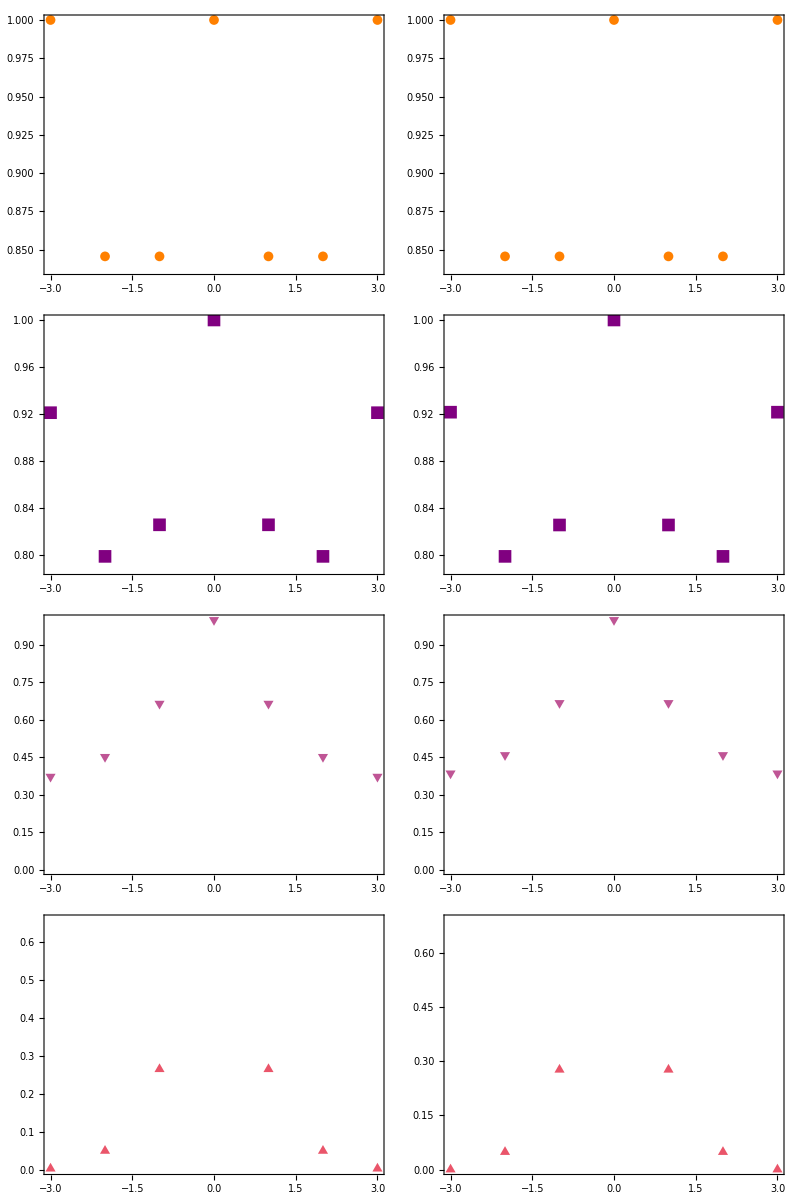

```mathematica
Grid[Reverse[spcPlots[[1]],2]]
(*Grid[Reverse[spcPlots[[2]],2]]*)
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head<>"r","/",
head<>"r","_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```

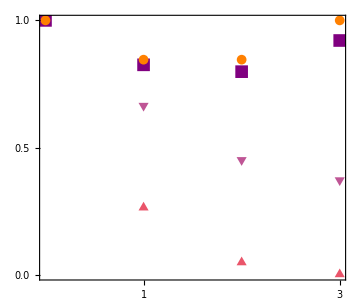

```mathematica
fs=22;
SetOptions[MaTeX,Magnification->1.75];
pltjoint=Legended[Show[Reverse[spcPlots[[1,;;,2]]],PlotRange->{{0,3},{0,1}},
FrameTicks->{LinTicks[-3,3,1,1],LinTicks[0,1,0.5,5],LinTicks[-3,3,1,1,ShowTickLabels->False],LinTicks[0,1,0.5,5,ShowTickLabels->False]},
Epilog->{
Inset[MaTeX["\\alpha = 0"],Scaled[{0.15, 0.1}]]
}
],
Placed[PointLegend[{Orange,Purple,Lighter[Blend[{Red,Purple},0.75]],Lighter[Blend[{Red,Purple},0.25]]},
MaTeX@Reverse[{"J_{\\perp} = 1.0","J_{\\perp} = 0.1","J_{\\perp} = 0.01","J_{\\perp} = 10^{-12} \\approx 0"}],
LegendMarkerSize->16,Spacings->0.0,
LegendMarkers->{{"●",10},{"■",13},{"▼",12},{"▲",12}}],
Right]
]
```

```mathematica
Export["plots/cn_0.png",pltjoint,ImageResolution->300]
```

plots/cn_0.png

```mathematica
(*Export["plots/cn.png",inplt,ImageResolution->300]*)
```

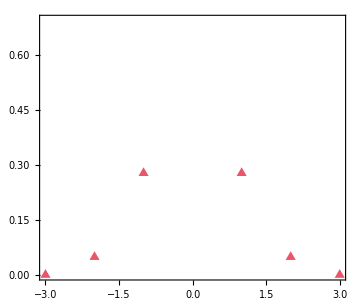

```mathematica
spcPlots[[1,4,1]]
```